# Simple Math

## Find The Root In Head

This simple program helps to play the trick “find the root in head.”
This can be done when a<1000 with exponent 2, 
or a<100 with exponent 3, 
or a<100 with exponent 41.

```mathematica
2^232
```

6901746346790563787434755862277025452451108972170386555162524223799296

```mathematica
a=RandomInteger[{100, 999}];
a^2
```

839056

```mathematica
a
```

916

## Some Plots

### The Sum, Difference, Product and Quotient of Two Functions

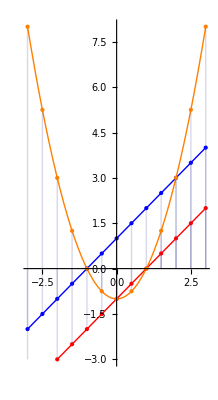

```mathematica
Clear[a, b, f, g]
f[x_]:=x-1;
g[x_]:=x+1;
a=-3;
b=3;
c=-3;
d=8;

ListPlot[f[x] g[x]/.x->Range[a, b, 0.5],Filling->Axis, PlotRange->{c, d}, DataRange->{a, b}, PlotStyle->Orange];
ListPlot[f[x]/.x->Range[a, b, 0.5],Filling->Axis, PlotRange->{c, d}, DataRange->{a, b}, PlotStyle->Red];
ListPlot[g[x]/.x->Range[a, b, 0.5],Filling->Axis, PlotRange->{c, d}, DataRange->{a, b}, PlotStyle->Blue];
Plot[{f[x], g[x], f[x]g[x]}, {x, a, b}, PlotRange->{c, d}, PlotStyle->{Red, Blue, Orange}, AspectRatio->Automatic];
Show[%, %%, %%%, %%%%]
```

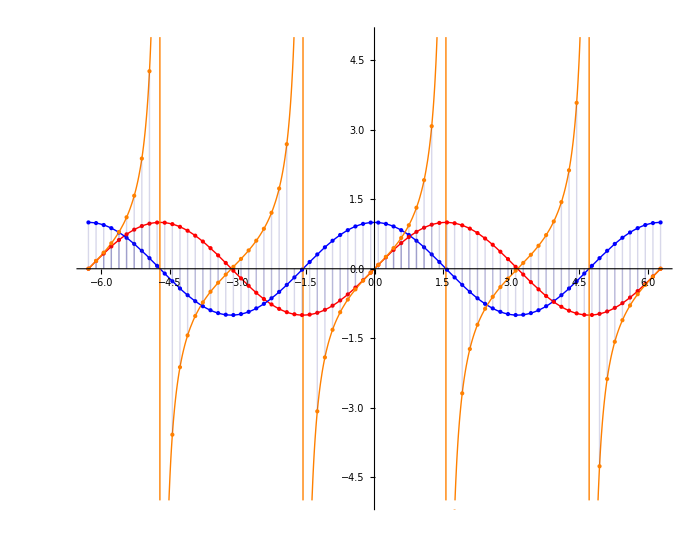

```mathematica
Clear[a, b, f, g]
f[x_]:=Sin[x];
g[x_]:=Cos[x];
a=-2π;
b=2π;
c=-5;
d=5;
m=75;
h=(b-a)/m;

ListPlot[f[x]/g[x]/.x->Range[a, b, h],Filling->Axis, PlotRange->{c, d}, DataRange->{a, b}, PlotStyle->Orange];
ListPlot[f[x]/.x->Range[a, b, h],Filling->Axis, PlotRange->{c, d}, DataRange->{a, b}, PlotStyle->Red];
ListPlot[g[x]/.x->Range[a, b, h],Filling->Axis, PlotRange->{c, d}, DataRange->{a, b}, PlotStyle->Blue];
Plot[{f[x], g[x], f[x]/g[x]}, {x, a, b}, PlotRange->{c, d}, PlotStyle->{Red, Blue, Orange}, AspectRatio->Automatic, ImageSize->700];
Show[%, %%, %%%, %%%%]
```

### Reflection

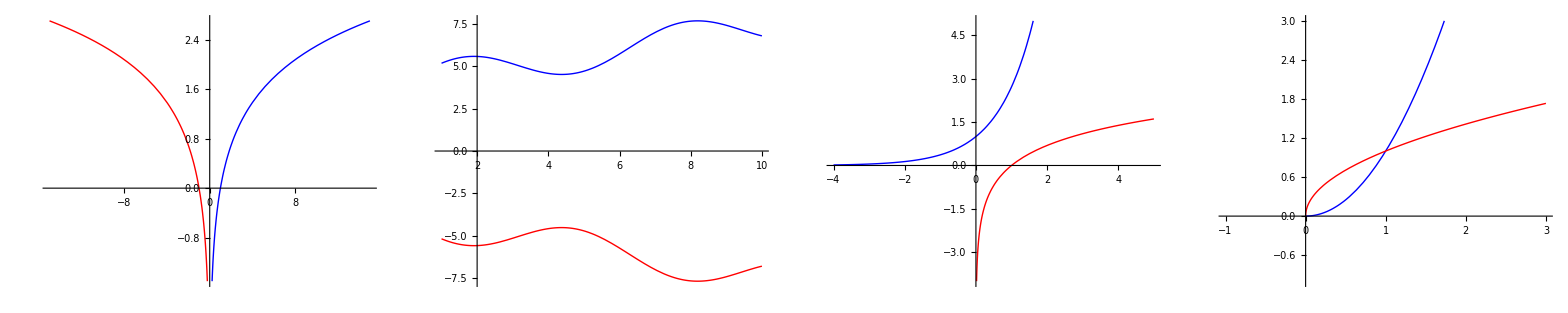

```mathematica
{{Plot[{Log[x], Log[-x]}, {x, -15, 15}, PlotStyle->{Blue, Red}], 
Plot[{4+x/3+Sin[x], -(4+x/3+Sin[x])}, {x, 1, 10}, PlotStyle->{Blue, Red}],
Plot[{ⅇ^x, Log[x]}, {x, -4, 5}, PlotRange->{-4, 5}, AspectRatio->1, PlotStyle->{Blue, Red}],
Plot[{If[x>0,x^2], √x}, {x, -1, 3}, PlotRange->{-1, 3}, AspectRatio->1, PlotStyle->{Blue, Red}]}}//TableForm
```

### Scaling

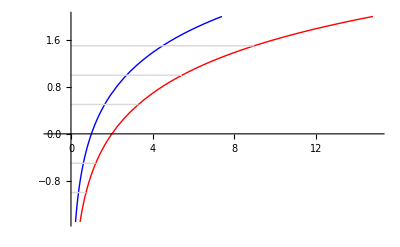

```mathematica
Plot[{
If[0<x<7.5, Log[x]], 
If[0<x<15, Log[x/2]], 
If[0<x<2 ⅇ^0.5, 0.5], 
If[0<x<2ⅇ, 1], 
If[0<x<2 ⅇ^1.5, 1.5], 
If[0<x<2 ⅇ^-0.5, -0.5], 
If[0<x<2 ⅇ^-1, -1]}, {x, -1, 15}, PlotRange->{-1.5, 2}, PlotStyle->{Blue, Red, LightGray, LightGray, LightGray, LightGray, LightGray}]
```

### Translation

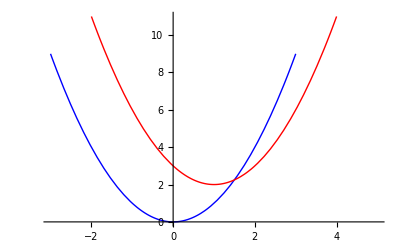

```mathematica
Plot[{If[-3<x<3, x^2], If[-2<x<4, ((x-1)^2+2)]}, {x, -3, 5}, PlotStyle->{Blue, Red}]
```

### Simpson’s Rule

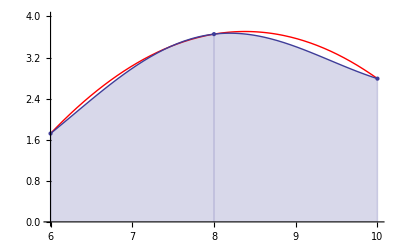

```mathematica
Clear[a, b, f];
a=6;
b=10;
f[x_]:=x/3+Sin[x];

Plot[f[x], {x, a,b}, PlotRange->{0, 4}, Filling->Bottom];
ListPlot[f/@{a, (a+b)/2, b}, DataRange->{a, b}, PlotRange->{0, 4}, Filling->Bottom];
Plot[InterpolatingPolynomial[{{a, f[a]}, {b, f[b]}, {(a+b)/2, f[(a+b)/2]}}, x]//Evaluate, {x, a, b}, PlotStyle->Red, PlotRange->{0, 4}];
Show[%, %%, %%%]
```

-1/6 (a-b) (f[a]+f[b]+4 f[(a+b)/2])

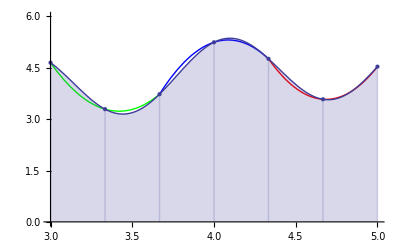

```mathematica
Clear[a, b, f, m, h, j, i]

Integrate[
InterpolatingPolynomial[
{{a, f[a]}, {b, f[b]}, {(a+b)/2, f[(a+b)/2]}}
, x]
, {x, a, b}]

a=3;
b=5;
m=3;
f[x_]:=x/3+Sin[5x]+3;

h=(b-a)/(2m);

ListPlot[f[Range[a, b, h]], PlotRange->{0, 6}, Filling->Bottom, DataRange->{a, b}];
Plot[f[x], {x, a, b}, PlotRange->{0, 6}, Filling->Bottom];

tt=Transpose/@({Table[Take[RotateLeft[Range[a, b, h], 2i], 3], {i, 0, m-1}], 
f/@Table[Take[RotateLeft[Range[a, b, h], 2i], 3], {i, 0, m-1}]}//Transpose);

Table[
Plot[
If[a-2h+2j h<x<a+2j h, 
InterpolatingPolynomial[tt[[j]], x]]
, {x, a, b},PlotRange->{0, 6},  PlotStyle->Hue[j/m]]
, {j,  m}];

Show[%, %%%, %%%%]
```

### Midpoint Rule

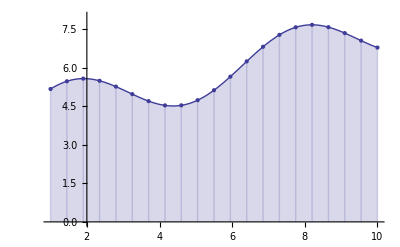

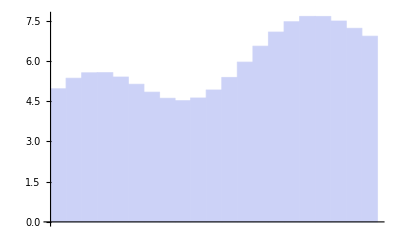

```mathematica
Clear[a, b, f, m, h];
a=1;
b=10;
m=20;
f[x_]:=4+x/3+Sin[x];


h=(b-a)/m;

Plot[f[x], {x, a, b}, PlotRange->{0, 8}, Filling->Bottom];
ListPlot[f[Range[a, b, h]], PlotRange->{0, 8}, Filling->Axis, DataRange->{a, b}];
Show[%, %%]
BarChart[f[Range[a-h/2, b, h]],BarSpacing->None]
```

### Plot In The Polar Coordinate System

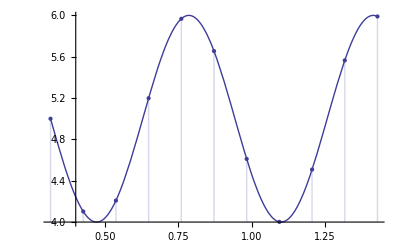

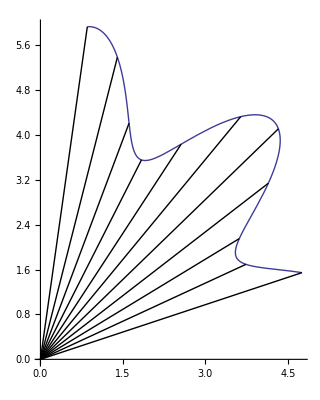

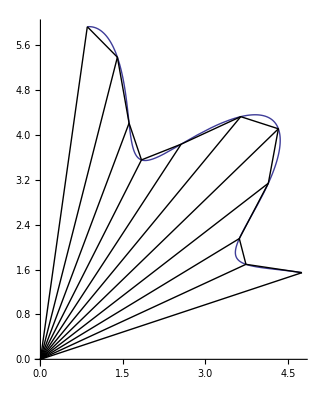

```mathematica
Clear[a, b, n, f];

a=π/10;
b=5π/11; (* 角度範圍 *)
n=10; (* a 到 b 之間切了幾個角度 *)
f[x_]:=5+Sin[10x];

Plot[f[x],{x,a,b}];
ListPlot[f[Range[a,b, (b-a)/n]], DataRange->{a, b}, Filling->Axis];
Show[%, %%]

Graphics[Line/@({Table[{0, 0}, {n+1}], {f[Range[a,b, (b-a)/n]]Cos[Range[a,b, (b-a)/n]], 
f[Range[a,b,(b-a)/n]]Sin[Range[a,b, (b-a)/n]]}//Transpose}//Transpose)];
PolarPlot[f[x],{x,a,b}];
Show[%, %%]


Graphics[Line/@({Table[{0, 0}, {n+1}], {f[Range[a,b, (b-a)/n]]Cos[Range[a,b, (b-a)/n]], 
f[Range[a,b, (b-a)/n]]Sin[Range[a,b, (b-a)/n]]}//Transpose}//Transpose)];
{f[Range[a,b, (b-a)/n]]Cos[Range[a,b, (b-a)/n]], 
f[Range[a,b, (b-a)/n]]Sin[Range[a,b, (b-a)/n]]}//Transpose//Line//Graphics;
PolarPlot[f[x],{x,a,b}];
Show[%, %%, %%%]
```

## Magic Square of Order 3

Put 1, 2, 3, ..., 9 into different cells such that the sums of the 3 numbers of all rows, all columns, and both diagonals are the same. 
The answer is well-known, but the derivation is not. 
Here is the derivation.

```mathematica
Graphics[
Table[{EdgeForm[Thin], White, Rectangle[{i, j}]}, {i, 3}, {j, 3}]
, ImageSize->Small]
```

-Graphics-

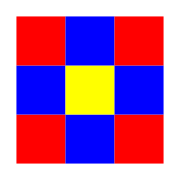

```mathematica
Graphics[
Table[{
Which[
(i==1&&j==1)||(i==1&&j==3)||(i==3&&j==1)||(i==3&&j==3) , Red, 
(i==1&&j==2)||(i==2&&j==1)||(i==3&&j==2)||(i==2&&j==3) , Blue, 
(i==2&&j==2) , Yellow
],
Rectangle[{i, j}]}, {i, 3}, {j, 3}]
, ImageSize->Small]
```

Let a be the number in the yellow cell, 
b be the sum of all numbers in the blue cells, 
and c be the sum of all numbers in the red cells. 

Since the sum of all 9 numbers equals 45, the numbers in every row (column) have the sum 15. 
Thus, we have 

4a+3b+2c=120
a+b+c=45
2a+b=30

and hence a=5, b=c=20. 

Now that a=5, we look for all pairs of numbers that have the sum 10. 
There are 4 such pairs. 
Find 3 numbers from 3 different pairs such that their sum is 15. 
There are 4 this kind of tuples. 
They are just the four edges of the square. 

The above argument only works for order 3.

## Catenary & Parabola

It’s said (by Johann Bernoulli) that Jacob Bernoulli thought a catenary is a parabola. 
Here is the plots of both.

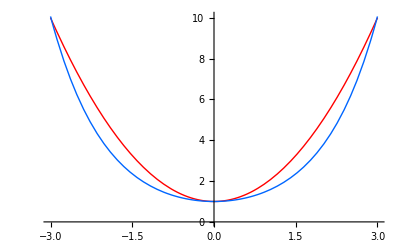

```mathematica
Plot[{x^2+1, (ⅇ^x+ⅇ^-x)/2}, {x, -3, 3}, PlotStyle->{Hue[0], Hue[.6]}]
```

## 8 Perfect Faro Shuffles

It’s said that if a deck is perfectly shuffled eight times, the cards will be in the same order as they were before the shuffling.
Here is an experiment on it.

```mathematica
(* shuffle function *)
Clear[f, aaa];
f[aaa_]:=({aaa[[Range[1, Length[aaa]/2]]], Table[0, {Length[aaa]/2}]}//Transpose//Flatten)+
({aaa[[Range[Length[aaa]/2+1, Length[aaa]]]], Table[0, {Length[aaa]/2}]}//Transpose//Flatten//RotateRight);
```

```mathematica
(* before shuffling *)
bbb=Range[52]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

```mathematica
(* after one shuffle *)
f[bbb]
```

{1,27,2,28,3,29,4,30,5,31,6,32,7,33,8,34,9,35,10,36,11,37,12,38,13,39,14,40,15,41,16,42,17,43,18,44,19,45,20,46,21,47,22,48,23,49,24,50,25,51,26,52}

```mathematica
(* after 8 shuffles *)
bbb//f//f//f//f//f//f//f//f
%==bbb
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

True

```mathematica
(* of course, if there are more (or less) than 52 cards, the statement would fail *)
ccc=Range[54];
ccc//f//f//f//f//f//f//f//f
%==ccc
```

{1,48,42,36,30,24,18,12,6,53,47,41,35,29,23,17,11,5,52,46,40,34,28,22,16,10,4,51,45,39,33,27,21,15,9,3,50,44,38,32,26,20,14,8,2,49,43,37,31,25,19,13,7,54}

False